```mathematica
Needs["OpenCLLink`"]
```

```mathematica
openclCode=ReadString[FileNameJoin[{NotebookDirectory[],"OpenCLMonteCarlo_BilayerGraphene.cl"}]];
```

```mathematica
rng=OpenCLFunctionLoad[openclCode,"RNGtest",{{"Float","Output"},{"Integer32","Input"}},100,"ShellOutputFunction"->Print];
values=ConstantArray[0,500];
seeds=RandomInteger[{362436000,562436000},500];
Mean[rng[values,seeds][[1]]]
StandardDeviation[rng[values,seeds][[1]]]
PearsonChiSquareTest[rng[values,seeds][[1]],UniformDistribution[]]
```

0.518201

0.293494

0.45021

```mathematica
(* Dimension units*)
EvToErg=1.6*10^-12;
k=1.38*10^-16 ;(*Boltzmann constant*)
c=3*10^10; (*Speed of light*)
T=100 ;(*Temperature*)
Dak=18*EvToErg;(* Acoustic phonon constant*)
Dopt=1.4*10^9*EvToErg; (*Optic phonon constant*)
ℏ=10^-27 ;(* Dirak constant*)
ρ=2*7.7*10^-8 ;(* Surface dens*)
vs=2.6*10^6 ;(* Speed of sound*)
e=4.8*10^-10 ;(* Electron charge*)
vf=10^8 ;(* Speed of Fermi*)
n0=10^12; (* 2D concentration*)
eph=0.196*EvToErg;(* Optic phonon energy*)
γ=0.35*EvToErg;
Δ=0.1*EvToErg; 
Δ1=Sqrt[γ^2/2+Δ^2];
Δ2=γ/Sqrt[2];
Δ3=Sqrt[γ^2+4 Δ^2];
νac=(k*T*Dak)^2/(2*ℏ^3*ρ*vs^2*vf^2);
νopt=k*T*Dopt^2/(4*ℏ*ρ*eph*vf^2);
νrad = 1;
```

```mathematica
ω = 5 νac;
ϕ = π/6;
Ex=5;
Ey=5;
Exc=0;
Eyc=0;
H = 0;
```

```mathematica
HSGS=k*T*νac*c/e/vf^2;
HSI=HSGS/10000.0;
ESGS=k*T*νac/e/vf;
ESI=ESGS*300.0;
jSGS=n0*vf*e;
powerSGS=jSGS*ESGS;
power0Etau=n0*e^2*vf^2/γ;
```

```mathematica
n = 100;
fun=OpenCLFunctionLoad[openclCode,"jobKernel",{{"Float","Output"},{"Integer32","Output"},{"Integer32","Output"},{"Float","Input"},{"Integer32","Input"}},n];
values=Table[0,{i,n}];
numcols=Table[0,{i,n}];
upcols=Table[0,{i,n}];
params=Table[0,{i,19}];
```

```mathematica
outmas={};
VarName="Ex";
IterMessage="Solve is run!";
Dynamic[IterMessage]
gb=AbsoluteTime[];
For[var=0,var≤10,var+=0.5,
b=AbsoluteTime[];
(*Parameters*)
params[[1]]=Exc / ESGS;(*Exc*)
params[[2]]=Eyc/ESGS;(*Eyc*)
params[[3]]=var/ESGS;(*Ex*)
params[[4]]=Ey/ESGS;(*Ey*)
params[[5]]=H/HSGS;(*H*)
params[[6]]=ω/νac;(*wx*)
params[[7]]=ω/νac;(*wy*)
params[[8]]=ϕ;(*phi*)
params[[9]]=1;(*wla_max*)
params[[10]]=νopt/νac;(*wlo_max*)
params[[11]]=νrad/νac;(*light_max*)
params[[12]]=eph/k/T;(*Subscript[ℏω, 0]*)
params[[13]]=ℏ ω/k/T;(*ℏω*)
params[[14]]=Δ1/k/T;(*Δ1*)
params[[15]]=Δ2/k/T;(*Δ2*)
params[[16]]=Δ3/k/T;(*Δ3*)
params[[17]]=Min[0.001/Max[params[[1;;5]]], 0.1/params[[6]]];(*step_time*)
params[[18]]=100000 * params[[17]];(*all_time*)
params[[19]]=ℏ/k/T/10^-13;(*Δϵ поиграться с ней*)
(*Solve*)
count=20;
out={};
Do[
seeds=RandomInteger[{100000000,1000000000},n];
res=fun[values,numcols,upcols,params,seeds];
AppendTo[out,res];
,{k,count}
];
res=Mean[out];
tau=params[[18]]/Mean[res[[2]]]/νac;
power0=power0Etau*tau*(params[[3]]*ESGS)^2;
Omega=2*e*vf^2*h/c/γ;
AppendTo[outmas,{var,Mean[res[[1]]],Mean[res[[2]]],Mean[res[[3]]],StandardDeviation[res[[1]]],Δ/γ,γ/k/T,Omega,tau,(params[[6]]+params[[7]])/2*νac}];
e=AbsoluteTime[];
IterMessage=VarName<>" = "<>ToString[N[var]]<>" solve for "<>ToString[e-b]<>" second(s)";
];
ge=AbsoluteTime[];
IterMessage="Solve is over for "<>ToString[ge-gb]<>" second(s)";
```

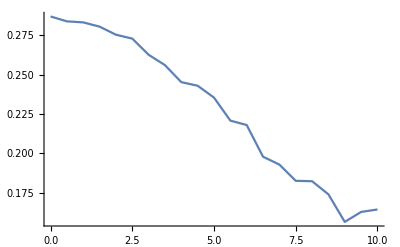

```mathematica
ListPlot[{outmas[[All,1;;2]]},Joined->True,InterpolationOrder->1,PlotRange->All]
```

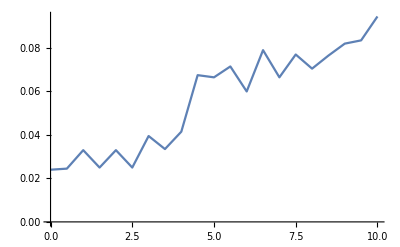

```mathematica
ListLinePlot[ outmas[[All,{1,4}]],Joined->True,InterpolationOrder->1,PlotRange->All]
```

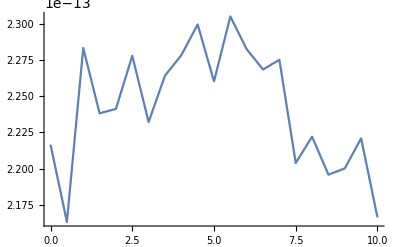

```mathematica
ListLinePlot[outmas[[All,{1,9}]],Joined->True,InterpolationOrder->1,PlotRange->All]
```

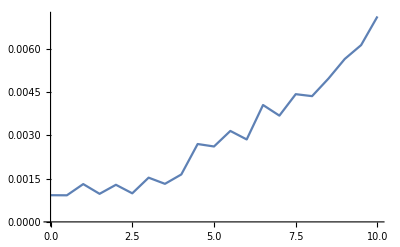

```mathematica
ListLinePlot[Transpose[{outmas[[All,1]],outmas[[All,4]]/outmas[[All,3]]}],Joined->True,InterpolationOrder->1,PlotRange->All]
```